#### Preamble

```mathematica
ClearAll@@{$Context<>"*"}
SetDirectory[NotebookDirectory[]]
saveTask=CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],15*60]; 
StartScheduledTask[saveTask] (*Saves nb each 15 minutes*) ;

<<"MaTeX`"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Maxima_Minima.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Optics_Mie.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Optical_functions/Au_JohnsnChristy.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/jet_jet-extended.wls"
```

/home/juanathan/Documentos/MSc_Thesis/3-FEM-Calc/3-Incrusted

#### Plots format

```mathematica
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);
colors[[1]] = ColorData[3,2];
PrependTo[colors,Black];
```

```mathematica
fs=9;
cdata3 = Table[ColorData[3,i],{i,10}];cdata3[[3]] = Purple;
texStyle:={FontFamily->"Latin Modern Roman",FontSize->fs,Black};
```

```mathematica
graphsOpts:={Mesh->Full,BaseStyle->texStyle,Frame->True,FrameStyle->Black,ImageSize->215,PlotStyle->colors}
graphsOptsDash:={Mesh->Full,BaseStyle->texStyle,Frame->True,FrameStyle->Black,ImageSize->215,PlotStyle->Table[Directive[Dashed,colors[[i]]],{i,10}]}
```

```mathematica
graphsOptsPolar:={Mesh->30,BaseStyle->texStyle,PolarAxes->True,FrameStyle->Black,ImageSize->215,
	PlotStyle->Table[Directive[PointSize[.015],colors[[i]]],{i,10}],PolarGridLines->Automatic,Joined->True,GridLinesStyle->Directive[Gray,Opacity[.1]],
	PolarAxesOrigin->{{Left,Up},Automatic}}
graphsOptsPolarDashed:={Mesh->30,BaseStyle->texStyle,PolarAxes->True,FrameStyle->Black,ImageSize->215,
	PlotStyle->Table[Directive[Dashed,PointSize[.015],colors[[i]]],{i,10}],PolarGridLines->Automatic,Joined->True,GridLinesStyle->Directive[Gray,Opacity[.1]],
	PolarAxesOrigin->{{Left,Up},Automatic}}
```

```mathematica
graphsOptsDensity := { BaseStyle -> texStyle, FrameStyle -> Black, PlotRange -> Full,  ColorFunctionScaling -> True, ColorFunction -> JetExtended, Mesh -> None, ImageSize -> 150, PlotRangePadding -> None  }
```

#### Sorting Functions

```mathematica
maxPair[list_,ind_]:= SortBy[list, #[[ind]]&][[-1,{1,ind}]]
makePairs[list_,ind_]:=Map[Table[#[[;;,{1,i}]],{i,ind}]&,list]
```

Efficiencies (Normal Scale)

```mathematica
scaling = None
```

None

### Mie

```mathematica
radius = 12.5;
nNP=JohnsonChristyAuRefSize[#,radius]&;
wlength=Range[400,600,2.5];
max=scaQ=extQ={0,0};

scaFunc[lda_]:=Map[MieScatteringQ[{nMat[#],nNP[#]},#,radius]&,toMap[lda]];
extFunc[lda_]:=Map[MieExtinctionQ[{nMat[#],nNP[#]},#,radius]&,toMap[lda]];
```

```mathematica
i=1;
nMat=1.&;
extQ[[i]]=extFunc[wlength];
scaQ[[i]]=scaFunc[wlength];
max[[i]]=FindExtrema[#,wlength[[{1,-1}]],10.,"Maxima"][[1,1]]&/@{extFunc,scaFunc};

i++;
nMat=1.5&;
extQ[[i]]=extFunc[wlength];
scaQ[[i]]=scaFunc[wlength];
max[[i]]=FindExtrema[#,wlength[[{10,-1}]],10.,"Maxima"][[1,1]]&/@{extFunc,scaFunc};

max=Reverse@Transpose[max];
```

```mathematica
mie=MapThread[Show[{ListPlot[#,DataRange->wlength[[{1,-1}]],Joined->True,Filling->{1->{2}},ScalingFunctions->scaling,PlotStyle->{Directive[Thick,Dashed,Green],Directive[Thick,Dashed,Green]}],
ListPlot[Callout[#,ToString[IntegerPart@#[[1]]],Left]&/@#2,ScalingFunctions->scaling]},PlotRange->All]&,{{scaQ,extQ-scaQ},max}]
```

{-Graphics-,-Graphics-}

### Interface

```mathematica
cases = {7,6,5,1,2,3,4};
data = FileNames["1*","*s"];
data = data[[#]]&/@cases;
 data//TableForm
data =Drop[Import[#,"Data"],5]&/@ data;

cases = {2,5,8,11};
maxPointsS =Transpose@Table[maxPair[data[[#1,10;;]],#2]&[i,j],{i,Length[data]},{j,cases}] ;
dataS =Transpose@makePairs[data,cases](*angle, h,wlenth, Q*);
maxPointsA =Transpose@Table[maxPair[data[[#1,10;;]],#2]&[i,j],{i,Length[data]},{j,cases+1}] ;
dataA =Transpose@makePairs[data,cases+1](*angle, h,wlenth, Q*);
```

Internal-s/1-Efficiencies-p75.csv
Internal-s/1-Efficiencies-p50.csv
Internal-s/1-Efficiencies-p25.csv
Internal-s/1-Efficiencies-00.csv
Internal-s/1-Efficiencies-m25.csv
Internal-s/1-Efficiencies-m50.csv
Internal-s/1-Efficiencies-m75.csv

```mathematica
dataA//Dimensions
```

{4,7,44,2}

```mathematica
plots = {0,0};
mieAll = Transpose[{mie,mie,mie,mie}];

Map[ListPlot[#,PlotMarkers-> "●",Mesh->None,Evaluate[graphsOpts],Joined->True,ScalingFunctions->scaling]&,dataA];
Map[ListPlot[Callout[#,ToString[NumberForm[N[#[[1]]],{4,1}]],Below]&/@#,PlotStyle->Directive[PointSize[.02],Blue],ScalingFunctions->scaling, Joined->True]& @ #&,maxPointsA];
plots[[2]] = MapThread[Show,{%%,%}];

Map[ListPlot[#,PlotMarkers-> "○",Mesh->None,Evaluate[graphsOptsDash],Joined->True,ScalingFunctions->scaling]&,dataS];
Map[ListPlot[Callout[#,ToString[NumberForm[N[#[[1]]],{4,1}]],Below]&/@#,PlotStyle->Directive[PointSize[.02],Blue],ScalingFunctions->scaling,Joined->True]& @ #&,maxPointsS];
plots[[1]] = MapThread[Show,{%%,%}];
MapThread[Show,{plots,mieAll},2]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

Efficiencies (Log Scale)

```mathematica
scaling = "Log"
```

Log

### Mie

```mathematica
radius = 12.5;
nNP=JohnsonChristyAuRefSize[#,radius]&;
wlength=Range[400,600,2.5];
max=scaQ=extQ={0,0};

scaFunc[lda_]:=Map[MieScatteringQ[{nMat[#],nNP[#]},#,radius]&,toMap[lda]];
extFunc[lda_]:=Map[MieExtinctionQ[{nMat[#],nNP[#]},#,radius]&,toMap[lda]];
```

```mathematica
i=1;
nMat=1.&;
extQ[[i]]=extFunc[wlength];
scaQ[[i]]=scaFunc[wlength];
max[[i]]=FindExtrema[#,wlength[[{1,-1}]],10.,"Maxima"][[1,1]]&/@{extFunc,scaFunc};

i++;
nMat=1.5&;
extQ[[i]]=extFunc[wlength];
scaQ[[i]]=scaFunc[wlength];
max[[i]]=FindExtrema[#,wlength[[{10,-1}]],10.,"Maxima"][[1,1]]&/@{extFunc,scaFunc};

max=Reverse@Transpose[max];
```

```mathematica
mie=MapThread[Show[{ListPlot[#,DataRange->wlength[[{1,-1}]],Joined->True,Filling->{1->{2}},ScalingFunctions->scaling,PlotStyle->{Directive[Thick,Dashed,Green],Directive[Thick,Dashed,Green]}],
ListPlot[Callout[#,ToString[IntegerPart@#[[1]]],Left]&/@#2,ScalingFunctions->scaling]},PlotRange->All]&,{{scaQ,extQ-scaQ},max}]
```

{-Graphics-,-Graphics-}

### Interface

```mathematica
cases = {7,6,5,1,2,3,4};
data = FileNames["1*","*s"];
data = data[[#]]&/@cases;
 data//TableForm
data =Drop[Import[#,"Data"],5]&/@ data;

cases = {2,5,8,11};
maxPointsS =Transpose@Table[maxPair[data[[#1,10;;]],#2]&[i,j],{i,Length[data]},{j,cases}] ;
dataS =Transpose@makePairs[data,cases](*angle, h,wlenth, Q*);
maxPointsA =Transpose@Table[maxPair[data[[#1,10;;]],#2]&[i,j],{i,Length[data]},{j,cases+1}] ;
dataA =Transpose@makePairs[data,cases+1](*angle, h,wlenth, Q*);
```

Internal-s/1-Efficiencies-p75.csv
Internal-s/1-Efficiencies-p50.csv
Internal-s/1-Efficiencies-p25.csv
Internal-s/1-Efficiencies-00.csv
Internal-s/1-Efficiencies-m25.csv
Internal-s/1-Efficiencies-m50.csv
Internal-s/1-Efficiencies-m75.csv

```mathematica
plots = {0,0};
mieAll = Transpose[{mie,mie,mie,mie}];

Map[ListPlot[#,PlotMarkers-> "●",Mesh->None,Evaluate[graphsOpts],Joined->True,ScalingFunctions->scaling]&,dataA];
Map[ListPlot[Callout[#,ToString[NumberForm[N[#[[1]]],{4,1}]],Below]&/@#,PlotStyle->Directive[PointSize[.02],Blue],ScalingFunctions->scaling, Joined->True]& @ #&,maxPointsA];
plots[[2]] = MapThread[Show,{%%,%}];

Map[ListPlot[#,PlotMarkers-> "○",Mesh->None,Evaluate[graphsOptsDash],Joined->True,ScalingFunctions->scaling]&,dataS];
Map[ListPlot[Callout[#,ToString[NumberForm[N[#[[1]]],{4,1}]],Below]&/@#,PlotStyle->Directive[PointSize[.02],Blue],ScalingFunctions->scaling,Joined->True]& @ #&,maxPointsS];
plots[[1]] = MapThread[Show,{%%,%}];
plots
plotsMie =MapThread[Show,{plots,mieAll},2];
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
MapThread[Show[{#1,#2},PlotRange->{Log[.0005],Log[5]},Axes->False,AspectRatio->1.5]&,plotsMie,1]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Near Field Abs -- 15

```mathematica
cases = {7,6,5,1,2,3,4};
data = FileNames["2*"~~"*15*","*s"];
data = data[[#]]&/@cases;
data//TableForm

data =Drop[Import[#,"Data"],8]&/@ data;
lim = radius*4;
```

Internal-s/2-Near-15-p75.csv
Internal-s/2-Near-15-p50.csv
Internal-s/2-Near-15-p25.csv
Internal-s/2-Near-15-00.csv
Internal-s/2-Near-15-m25.csv
Internal-s/2-Near-15-m50.csv
Internal-s/2-Near-15-m75.csv

```mathematica
max = Max[data[[;;,;;,4]]] (*To normalize all cases*)
case = ConstantArray[-1,7] (*To place above or below the glass*)

dataX = Table[Select[data[[i]], Abs[#[[2]]]<.001   &],{i,Length[data]}];
dataX = MapThread[#1/. {x_,y_,z_,norm_} -> {x, #2 * z, norm/max} &,{dataX, case}];
dataX = Table[Select[dataX[[i]], (Abs[#[[1]]]<lim && Abs[#[[2]]]<lim) &],{i,Length[dataX]}];

dataY = Table[Select[data[[i]], Abs[#[[1]]]<.001   &],{i,Length[data]}];
dataY = MapThread[#/. {x_,y_,z_,norm_} -> {y, #2 * z, norm/max} &, {dataY, case}];
dataY = Table[Select[dataY[[i]], (Abs[#[[1]]]<lim && Abs[#[[2]]]<lim) &],{i,Length[dataY]}];
```

5.42853

{-1,-1,-1,-1,-1,-1,-1}

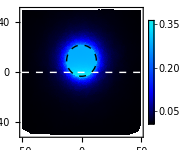
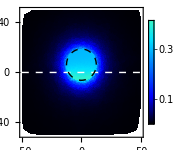
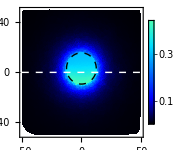
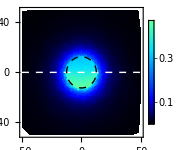
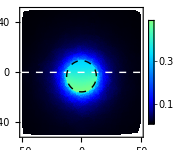
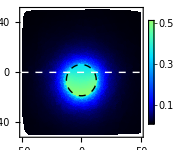
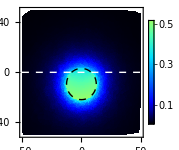

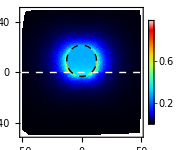

```mathematica
case = Table[i,{i,.75,-.75,-.25}];
system = {White,Dashed, Line[{{-lim,0},{lim,0}}],Black, Circle[{0,radius*#},radius]}&/@case;

plotsX = MapThread[ListDensityPlot[#1,ColorFunctionScaling->False,Evaluate[graphsOptsDensity], Epilog->#2, PlotLegends->Automatic]&, {dataX,system}]
plotsY = MapThread[ListDensityPlot[#1,ColorFunctionScaling->False,Evaluate[graphsOptsDensity], Epilog->#2, PlotLegends->Automatic]&, {dataY,system}]
```

Near Field Abs -- 38

```mathematica
cases = {7,6,5,1,2,3,4};
data = FileNames["2*"~~"*38*","*s"];
data = data[[#]]&/@cases;
data//TableForm

data =Drop[Import[#,"Data"],8]&/@ data;
lim = radius*4;
```

Internal-s/2-Near-38-p75.csv
Internal-s/2-Near-38-p50.csv
Internal-s/2-Near-38-p25.csv
Internal-s/2-Near-38-00.csv
Internal-s/2-Near-38-m25.csv
Internal-s/2-Near-38-m50.csv
Internal-s/2-Near-38-m75.csv

```mathematica
max = Max[data[[;;,;;,4]]] (*To normalize all cases*)
case = ConstantArray[-1,7] (*To place above or below the glass*)

dataX = Table[Select[data[[i]], Abs[#[[2]]]<.001   &],{i,Length[data]}];
dataX = MapThread[#1/. {x_,y_,z_,norm_} -> {x, #2 * z, norm/max} &,{dataX, case}];
dataX = Table[Select[dataX[[i]], (Abs[#[[1]]]<lim && Abs[#[[2]]]<lim) &],{i,Length[dataX]}];

dataY = Table[Select[data[[i]], Abs[#[[1]]]<.001   &],{i,Length[data]}];
dataY = MapThread[#/. {x_,y_,z_,norm_} -> {y, #2 * z, norm/max} &, {dataY, case}];
dataY = Table[Select[dataY[[i]], (Abs[#[[1]]]<lim && Abs[#[[2]]]<lim) &],{i,Length[dataY]}];
```

5.39872

{-1,-1,-1,-1,-1,-1,-1}

```mathematica
case = Table[i,{i,.75,-.75,-.25}];
system = {White,Dashed, Line[{{-lim,0},{lim,0}}],Black, Circle[{0,radius*#},radius]}&/@case;

plotsX = MapThread[ListDensityPlot[#1,ColorFunctionScaling->False,Evaluate[graphsOptsDensity], Epilog->#2, PlotLegends->Automatic]&, {dataX,system}]
plotsY = MapThread[ListDensityPlot[#1,ColorFunctionScaling->False,Evaluate[graphsOptsDensity], Epilog->#2, PlotLegends->Automatic]&, {dataY,system}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Near Field Abs -- 42

```mathematica
cases = {7,6,5,1,2,3,4};
data = FileNames["2*"~~"*42*","*s"];
data = data[[#]]&/@cases;
data//TableForm

data =Drop[Import[#,"Data"],8]&/@ data;
lim = radius*4;
```

Internal-s/2-Near-42-p75.csv
Internal-s/2-Near-42-p50.csv
Internal-s/2-Near-42-p25.csv
Internal-s/2-Near-42-00.csv
Internal-s/2-Near-42-m25.csv
Internal-s/2-Near-42-m50.csv
Internal-s/2-Near-42-m75.csv

```mathematica
max = Max[data[[;;,;;,4]]] (*To normalize all cases*)
case = ConstantArray[-1,7] (*To place above or below the glass*)

dataX = Table[Select[data[[i]], Abs[#[[2]]]<.001   &],{i,Length[data]}];
dataX = MapThread[#1/. {x_,y_,z_,norm_} -> {x, #2 * z, norm/max} &,{dataX, case}];
dataX = Table[Select[dataX[[i]], (Abs[#[[1]]]<lim && Abs[#[[2]]]<lim) &],{i,Length[dataX]}];

dataY = Table[Select[data[[i]], Abs[#[[1]]]<.001   &],{i,Length[data]}];
dataY = MapThread[#/. {x_,y_,z_,norm_} -> {y, #2 * z, norm/max} &, {dataY, case}];
dataY = Table[Select[dataY[[i]], (Abs[#[[1]]]<lim && Abs[#[[2]]]<lim) &],{i,Length[dataY]}];
```

5.35661

{-1,-1,-1,-1,-1,-1,-1}

```mathematica
case = Table[i,{i,.75,-.75,-.25}];
system = {White,Dashed, Line[{{-lim,0},{lim,0}}],Black, Circle[{0,radius*#},radius]}&/@case;

plotsX = MapThread[ListDensityPlot[#1,ColorFunctionScaling->False,Evaluate[graphsOptsDensity], Epilog->#2, PlotLegends->Automatic]&, {dataX,system}]
plotsY = MapThread[ListDensityPlot[#1,ColorFunctionScaling->False,Evaluate[graphsOptsDensity], Epilog->#2, PlotLegends->Automatic]&, {dataY,system}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Near Field Abs -- 75

```mathematica
cases = {7,6,5,1,2,3,4};
data = FileNames["2*"~~"*-75-*","*s"];
data = data[[#]]&/@cases;
data//TableForm

data =Drop[Import[#,"Data"],8]&/@ data;
lim = radius*4;
```

Internal-s/2-Near-75-p75.csv
Internal-s/2-Near-75-p50.csv
Internal-s/2-Near-75-p25.csv
Internal-s/2-Near-75-00.csv
Internal-s/2-Near-75-m25.csv
Internal-s/2-Near-75-m50.csv
Internal-s/2-Near-75-m75.csv

```mathematica
max = Max[data[[;;,;;,4]]] (*To normalize all cases*)
case = ConstantArray[-1,7] (*To place above or below the glass*)

dataX = Table[Select[data[[i]], Abs[#[[2]]]<.001   &],{i,Length[data]}];
dataX = MapThread[#1/. {x_,y_,z_,norm_} -> {x, #2 * z, norm/max} &,{dataX, case}];
dataX = Table[Select[dataX[[i]], (Abs[#[[1]]]<lim && Abs[#[[2]]]<lim) &],{i,Length[dataX]}];

dataY = Table[Select[data[[i]], Abs[#[[1]]]<.001   &],{i,Length[data]}];
dataY = MapThread[#/. {x_,y_,z_,norm_} -> {y, #2 * z, norm/max} &, {dataY, case}];
dataY = Table[Select[dataY[[i]], (Abs[#[[1]]]<lim && Abs[#[[2]]]<lim) &],{i,Length[dataY]}];
```

5.25707

{-1,-1,-1,-1,-1,-1,-1}

```mathematica
case = Table[i,{i,.75,-.75,-.25}];
system = {White,Dashed, Line[{{-lim,0},{lim,0}}],Black, Circle[{0,radius*#},radius]}&/@case;

plotsX = MapThread[ListDensityPlot[#1,ColorFunctionScaling->False,Evaluate[graphsOptsDensity], Epilog->#2, PlotLegends->Automatic]&, {dataX,system}]
plotsY = MapThread[ListDensityPlot[#1,ColorFunctionScaling->False,Evaluate[graphsOptsDensity], Epilog->#2, PlotLegends->Automatic]&, {dataY,system}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Far Field (Normal X, All WaveLengths)

```mathematica
data =  FileNames["3*","*s"]; 
data = data[[#]]&/@cases;
data//TableForm
data =Drop[Import[#,"Data"],8]&/@ data;
data = Map[Partition[#,51]&,data]; (*Separete eat wlength value*)
```

Internal-s/3-Abs-FarX-p75.csv
Internal-s/3-Abs-FarX-p50.csv
Internal-s/3-Abs-FarX-p25.csv
Internal-s/3-Abs-FarX-00.csv
Internal-s/3-Abs-FarX-m25.csv
Internal-s/3-Abs-FarX-m50.csv
Internal-s/3-Abs-FarX-m75.csv

```mathematica
thTiks=Table[{i*Pi/180.,
Which[i≤90,(90-i)Degree,
i<= 180,""(*Mod[i,90]*),
i< 270,(90-Mod[i,90])Degree,
True, Mod[i,90]Degree
]},{i,0,360,15}];

arrows ={#3,Arrow[-#2*{{Cos[#1],Sin[#1]},.025{Cos[#1],Sin[#1]}}]}&;
```

```mathematica
ClearAll[arrowList]

max = Max[#[[;;,;;,2]]]&/@data;
caseDir = 90-{15, 38, 42,75}; (*To place the incoming wave direction*)
case = Table[i,{i,.75,-.75,-.25}];
arrowList[max_] := MapThread[arrows[#1 Degree,max*1.1,#2]&, {caseDir,colors[[;;4]]}]

MapThread[
ListPolarPlot[#1/.{theta_,rad_}-> {theta+Pi/2.,rad},PlotRange->#2*1.65,
PolarAxesOrigin->{{Left,Up},#2},
Evaluate[graphsOptsPolar],
PolarTicks->{thTiks[[;;-2]],Automatic},
Prolog->{LightBlue,Disk[{0,0},#2*1.65,{0,-Pi}],LightYellow,Disk[{0,#2*#3}/3.5,#2/3.5]},
Epilog->arrowList[#2]
]&,
{data,max,case}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
maxList = Max[#[[;;,;;,2]]]&/@data;
max = Max[max]
case = Table[i,{i,.75,-.75,-.25}];

MapThread[
ListPolarPlot[#1/.{theta_,rad_}-> {theta+Pi/2.,rad},PlotRange->max*1.65,
PolarAxesOrigin->{{Left,Up},max},
Evaluate[graphsOptsPolar],
PolarTicks->{thTiks[[;;-2]],Automatic},
Prolog->{LightBlue,Disk[{0,0}, max*1.65,{0,-Pi}],LightYellow,Disk[1*{0,max*#2}/3.5,max /3.5]},
Epilog->arrowList[max]
]&,
{data,case}]
```

3.6418

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Far Field (Normal Y, All WaveLengths)

```mathematica
data =  FileNames["4*","*s"]; 
data = data[[#]]&/@cases;
data//TableForm
data =Drop[Import[#,"Data"],8]&/@ data;
data = Map[Partition[#,51]&,data]; (*Separete eat wlength value*)
```

Internal-s/4-Abs-FarY-p75.csv
Internal-s/4-Abs-FarY-p50.csv
Internal-s/4-Abs-FarY-p25.csv
Internal-s/4-Abs-FarY-00.csv
Internal-s/4-Abs-FarY-m25.csv
Internal-s/4-Abs-FarY-m50.csv
Internal-s/4-Abs-FarY-m75.csv

```mathematica
thTiks=Table[{i*Pi/180.,
Which[i≤90,(90-i)Degree,
i<= 180,""(*Mod[i,90]*),
i< 270,(90-Mod[i,90])Degree,
True, Mod[i,90]Degree
]},{i,0,360,15}];

arrows ={#3,Arrow[-#2*{{Cos[#1],Sin[#1]},.025{Cos[#1],Sin[#1]}}]}&;
```

```mathematica
ClearAll[arrowList]

max = Max[#[[;;,;;,2]]]&/@data;
caseDir = 90-{15, 38, 42,75}; (*To place the incoming wave direction*)
case = Table[i,{i,.75,-.75,-.25}];
arrowList[max_] := MapThread[arrows[#1 Degree,max*1.1,#2]&, {caseDir,colors[[;;4]]}]

MapThread[
ListPolarPlot[#1/.{theta_,rad_}-> {theta+Pi/2.,rad},PlotRange->#2*1.65,
PolarAxesOrigin->{{Left,Up},#2},
Evaluate[graphsOptsPolar],
PolarTicks->{thTiks[[;;-2]],Automatic},
Prolog->{LightBlue,Disk[{0,0},#2*1.65,{0,-Pi}],LightYellow,Disk[{0,#2*#3}/3.5,#2/3.5]},
Epilog->arrowList[#2]
]&,
{data,max,case}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
maxList = Max[#[[;;,;;,2]]]&/@data;
max = Max[max]
case = Table[i,{i,.75,-.75,-.25}];

MapThread[
ListPolarPlot[#1/.{theta_,rad_}-> {theta+Pi/2.,rad},PlotRange->max*1.65,
PolarAxesOrigin->{{Left,Up},max},
Evaluate[graphsOptsPolar],
PolarTicks->{thTiks[[;;-2]],Automatic},
Prolog->{LightBlue,Disk[{0,0}, max*1.65,{0,-Pi}],LightYellow,Disk[1*{0,max*#2}/3.5,max /3.5]},
Epilog->arrowList[max]
]&,
{data,case}]
```

3.6418

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}